# Cosmomathica v1.0

Santiago Casas, 2018

This notebook demonstrates how to use the Cosmomathica package version 1.0

## Calling external programs

### Initialization

First, load the Cosmomathica package

```mathematica
Directory[]
```

/local/home/scasas

```mathematica
SetDirectory[NotebookDirectory[]]
```

/local/home/scasas/CosmoProjects/cosmomathica

```mathematica
ManToGif[man_,name_String,step_Integer]:=Export[name<>".gif",Import[Export[FileNameJoin[{NotebookDirectory[],"temp.avi"}],man],"ImageList"][[1;;-1;;step]]];
```

```mathematica
<<(NotebookDirectory[]<>"cosmomathica.m")
```

### CAMB

CAMB takes a lot of parameters. In Cosmomathica, most of them are being treated as options with default values while some of them are regular parameters that have to be specified. The distinction is arbitrary. These are the default options (see the CAMB documentation for details):

```mathematica
?CAMB
```

CAMB[OmegaC, OmegaB, h] :
provides an interface to CAMB by Antony Lewis and Anthony Challinor. It takes a few parameters as well as a number of options as input, and returns various cosmological quantities. The distinction between parameters and options is in principle arbitrary. However, since some physical parameters are often assumed to take on a default value, they are being interpreted as an option here. To see the default options, type `Options[CAMB]`.

```mathematica
Options[CAMB]
```

{MGflag→0,pureMGflag→1,altMGflag→1,QSAflag→1,mugammapar→2,musigmapar→1,QRpar→1,DEmodel→1,GRtrans→0.001,B1→0.,lambda12→0.,B2→0.,lambda22→0.,ss→4.,E11→0.,E22→0.,mu0→-1.,sigma0→0.,MGQfix→0.,MGRfix→0.,Qnot→1.,Rnot→1.,sss→0.,Lindergamma→0.545,betastar→0.,astar→0.5,xistar→0.001,beta0→1.,xi0→0.0001,DilS→0.24,DilR→1.,FR0→0.0001,FRn→1.,w0ppf→-1.,wappf→0.,Tcmb→2.7255,OmegaNu→0,OmegaK0→0.,YHe→0.24,MasslessNeutrinos→3.046,MassiveNeutrinos→0,NuMassDegeneracies→{0},NuMassFractions→{1},ScalarInitialCondition→adiabatic,NonLinear→pk,HalofitVersion→4,WantCMB→True,WantTransfer→True,WantCls→False,WantScalars→False,WantVectors→False,WantTensors→False,ScalarSpectralIndex→{0.96},ScalarRunning→{0},TensorSpectralIndex→{0},RatioScalarTensorAmplitudes→{1},ScalarPowerAmplitude→{2.1×10^-9},PivotScalar→0.05,PivotTensor→0.05,DoReionization→True,UseOpticalDepth→False,OpticalDepth→0.,ReionizationRedshift→10.,ReionizationFraction→1.,ReionizationDeltaRedshift→0.5,AccuracyBoost→2,TransferHighPrecision→True,TransferInterpMatterPower→False,WantZstar→True,WantZdrag→True,OutputNormalization→1,MaxEll→1500,MaxEtaK→4000.,MaxEtaKTensor→800.,MaxEllTensor→400,TransferKmax→5,TransferKperLogInt→50,TransferRedshifts→{0.},AccuratePolarization→True,AccurateReionization→False,AccurateBB→False,DoLensing→False,OnlyTransfers→False,DerivedParameters→True,MassiveNuMethod→best,debugIntFloats→False}

```mathematica
?MGflag
```

An option for CAMB/MGCAMB: 
          MG_flag = 0 :  default GR
          MG_flag = 1 :  pure MG models
          MG_flag = 2 :  alternative MG models
          MG_flag = 3 :  QSA models

```mathematica
?QSAflag
```

An option for CAMB/MGCAMB: 
QSA_flag = 1 : f(R)
QSA_flag = 2 : Symmetron      
QSA_flag = 3 : Dilaton
QSA_flag = 4 : Hu-Sawicki f(R)

```mathematica
?FR0
```

Parameter options for MGCAMB

```mathematica
?MasslessNeutrinos
```

An option for CAMB

```mathematica
?HalofitVersion
```

An option for CAMB. Integer number that chooses the Halofit version used in the non-linear matter power spectrum.
1: Original, 2: Bird, 3: Peacock, 4: Takahashi, 5: Mead, 6: Halo model, 7: Casarini,
8: Mead2015, 9: Winther-f(R)

```mathematica
?DEmodel
```

An option for CAMB/MGCAMB:
DE_model = 0 : LCDM
DE_model = 1 : wCDM        
DE_model = 2 : (w0,wa)CDM  
DE_model = 3 : user defined

Default values of some CAMB default options:

```mathematica
OptionValue[CAMB,#]&/@{MGflag,FR0,FRn, OmegaNu,MasslessNeutrinos,NuMassDegeneracies,NuMassFractions,ScalarSpectralIndex,ScalarPowerAmplitude,MaxEtaK,TransferKmax, HalofitVersion}
```

{0,0.0001,1.,0,3.046,{0},{1},{0.96},{2.1×10^-9},4000.,5,4}

Run the CAMB code (without lensing the scalar angular power spectrum will contain only three curves corresponding to C_TT, C_EE, C_TE - see the CAMB documentation for further information) with the transfer function for two different redshifts

```mathematica
redsub=Subdivide[0.,50.,99]
```

{0.,0.505051,1.0101,1.51515,2.0202,2.52525,3.0303,3.53535,4.0404,4.54545,5.05051,5.55556,6.06061,6.56566,7.07071,7.57576,8.08081,8.58586,9.09091,9.59596,10.101,10.6061,11.1111,11.6162,12.1212,12.6263,13.1313,13.6364,14.1414,14.6465,15.1515,15.6566,16.1616,16.6667,17.1717,17.6768,18.1818,18.6869,19.1919,19.697,20.202,20.7071,21.2121,21.7172,22.2222,22.7273,23.2323,23.7374,24.2424,24.7475,25.2525,25.7576,26.2626,26.7677,27.2727,27.7778,28.2828,28.7879,29.2929,29.798,30.303,30.8081,31.3131,31.8182,32.3232,32.8283,33.3333,33.8384,34.3434,34.8485,35.3535,35.8586,36.3636,36.8687,37.3737,37.8788,38.3838,38.8889,39.3939,39.899,40.404,40.9091,41.4141,41.9192,42.4242,42.9293,43.4343,43.9394,44.4444,44.9495,45.4545,45.9596,46.4646,46.9697,47.4747,47.9798,48.4848,48.9899,49.4949,50.}

```mathematica
redshifts=Reverse[redsub(*Range[0,50,0.1]*)(*Join~{20,100}*)]
```

{50.,49.4949,48.9899,48.4848,47.9798,47.4747,46.9697,46.4646,45.9596,45.4545,44.9495,44.4444,43.9394,43.4343,42.9293,42.4242,41.9192,41.4141,40.9091,40.404,39.899,39.3939,38.8889,38.3838,37.8788,37.3737,36.8687,36.3636,35.8586,35.3535,34.8485,34.3434,33.8384,33.3333,32.8283,32.3232,31.8182,31.3131,30.8081,30.303,29.798,29.2929,28.7879,28.2828,27.7778,27.2727,26.7677,26.2626,25.7576,25.2525,24.7475,24.2424,23.7374,23.2323,22.7273,22.2222,21.7172,21.2121,20.7071,20.202,19.697,19.1919,18.6869,18.1818,17.6768,17.1717,16.6667,16.1616,15.6566,15.1515,14.6465,14.1414,13.6364,13.1313,12.6263,12.1212,11.6162,11.1111,10.6061,10.101,9.59596,9.09091,8.58586,8.08081,7.57576,7.07071,6.56566,6.06061,5.55556,5.05051,4.54545,4.0404,3.53535,3.0303,2.52525,2.0202,1.51515,1.0101,0.505051,0.}

```mathematica
redzrang=Range[Length[redshifts]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
GRtrans/.Options[CAMB]
```

0.001

```mathematica
ClearAll[cambdata]
```

```mathematica
cambdata[0]=CAMB[0.25,0.05,0.67,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->4, MGflag->0]
```

{CAMB[age]→14.0639,17,CAMB[Transfer]→{{{5.14524×10^-6,507663.,507663.,676882.,676882.,0.,507663.,507663.,518387.,-0.60286,505819.,505819.,0.108228,8.66411×10^10},{5.6823×10^-6,507663.,507663.,676882.,676882.,0.,507663.,507663.,518387.,-0.60286,505819.,505819.,0.119525,7.10373×10^10},360,1},98,{{1},361,{1}}}}
 |  |  |  |

```mathematica
cambdata[1]=CAMB[0.25,0.05,0.67,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->4, MGflag->3, QSAflag->4, FR0->10^(-10), FRn->1, DEmodel->0]
```

{CAMB[age]→14.0639,CAMB[zstar]→1088.98,15,CAMB[PSnonlinear]→{{{5.14524×10^-6,0.0162504},{5.6823×10^-6,0.0178755},{6.27542×10^-6,0.0196631},{6.93045×10^-6,0.0216295},355,{4.77103,0.000846745},{4.86741,0.00080455},{4.96574,0.000764424},{5.06605,0.000726269}},{1},96,{1},{1}},CAMB[Transfer]→{1}}
 |  |  |  |

```mathematica
cambdata[2]=CAMB[0.25,0.05,0.67,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->4, MGflag->3, QSAflag->4, FR0->10^(-4), FRn->1, DEmodel->0, GRtrans->1.0]
```

{CAMB[age]→14.0639,17,CAMB[Transfer]→{{{5.14524×10^-6,507663.,507663.,676882.,676882.,0.,507663.,507663.,518387.,-0.60286,505819.,505819.,0.108228,8.66411×10^10},{5.6823×10^-6,507663.,507663.,676882.,676882.,0.,507663.,507663.,518387.,-0.60286,505819.,505819.,0.119525,7.10373×10^10},360,1},98,{{1},361,{1}}}}
 |  |  |  |

```mathematica
Do[
Print["ii:", ii];
cambdata[ii]=CAMB[0.25,0.05,0.67,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->9, MGflag->3, QSAflag->4, FR0->10^(-ii), FRn->1, DEmodel->0];
,{ii,{4,5,6}}]
```

ii:4

ii:5

ii:6

```mathematica
SetDirectory[NotebookDirectory[]]
```

/local/home/scasas/CosmoProjects/cosmomathica

```mathematica
CAMB["redshifts"]/.cambdata[0]
```

{50.,49.4949,48.9899,48.4848,47.9798,47.4747,46.9697,46.4646,45.9596,45.4545,44.9495,44.4444,43.9394,43.4343,42.9293,42.4242,41.9192,41.4141,40.9091,40.404,39.899,39.3939,38.8889,38.3838,37.8788,37.3737,36.8687,36.3636,35.8586,35.3535,34.8485,34.3434,33.8384,33.3333,32.8283,32.3232,31.8182,31.3131,30.8081,30.303,29.798,29.2929,28.7879,28.2828,27.7778,27.2727,26.7677,26.2626,25.7576,25.2525,24.7475,24.2424,23.7374,23.2323,22.7273,22.2222,21.7172,21.2121,20.7071,20.202,19.697,19.1919,18.6869,18.1818,17.6768,17.1717,16.6667,16.1616,15.6566,15.1515,14.6465,14.1414,13.6364,13.1313,12.6263,12.1212,11.6162,11.1111,10.6061,10.101,9.59596,9.09091,8.58586,8.08081,7.57576,7.07071,6.56566,6.06061,5.55556,5.05051,4.54545,4.0404,3.53535,3.0303,2.52525,2.0202,1.51515,1.0101,0.505051,0.}

```mathematica
(*psnl[0][zind_,kind_]:=((CAMB["PSnonlinear"]/.cambdata[0])[[zind,kind,2]])*)
```

```mathematica
(*psnl[4][zind_,kind_]:=((CAMB["PSnonlinear"]/.cambdata[4])[[zind,kind,2]])*)
```

```mathematica
(*cpknl0=(CAMB["PSnonlinear"]/.cambdata[0])[[-1,All,2]]*)
```

```mathematica
(*(psnl[0][33,#])&/@Range[Length@kvals[0]]*)
```

```mathematica
(*cpknl4=(CAMB["PSnonlinear"]/.cambdata[4])[[-1,All,2]]*)
```

```mathematica
(*(psnl[4][33,#])&/@Range[Length@kvals[0]]*)
```

```mathematica
(*cpknl0/cpknl4*)
```

```mathematica
cambdata[6][[All,1]]
```

{CAMB[age],CAMB[zstar],CAMB[rstar],CAMB[100thetastar],CAMB[zdrag],CAMB[rdrag],CAMB[kD],CAMB[100thetaD],CAMB[zEQ],CAMB[100thetaEQ],CAMB[H(z)],CAMB[sigma8(z)],CAMB[f(z)],CAMB[D+(z)],CAMB[CLscalar],CAMB[redshifts],CAMB[PSlinear],CAMB[PSnonlinear],CAMB[Transfer]}

```mathematica
ClearAll[kvals,psl, psnl, growth, growthrate, s8growth, s8growthrate, Hofz, redshiftsz]
```

```mathematica
Interrupt[]
```

$Aborted

```mathematica
ClearAll[ii]
```

```mathematica
Remove[ii]
```

```mathematica
totalmodlist={0,1,2,4,5,6}
```

{0,1,2,4,5,6}

```mathematica
Do[
redshiftsz[ii_]:=(CAMB["redshifts"]/.cambdata[ii]);
scalefactor[ii_][zind_]:=(1/redshiftsz[0][[zind]]);
kvals[ii_]:=((CAMB["PSlinear"]/.cambdata[ii])[[1,All,1]]);
psl[ii_][zind_,kind_]:=((CAMB["PSlinear"]/.cambdata[ii])[[zind,kind,2]]);
psnl[ii_][zind_,kind_]:=((CAMB["PSnonlinear"]/.cambdata[ii])[[zind,kind,2]]);
growth[ii_][zind_,kind_]:=(((CAMB["Transfer"]/.cambdata[ii])[[zind, kind,7]])/((CAMB["Transfer"]/.cambdata[ii])[[-1, kind,7]]));
growthrate[ii_][zind_,kind_]:=((CAMB["Transfer"]/.cambdata[ii])[[zind, kind,14]])/((CAMB["Transfer"]/.cambdata[ii])[[1, kind,14]]);
s8growth[ii_][zind_]:=((CAMB["D+(z)"]/.cambdata[ii])[[zind]]);
s8growthrate[ii_][zind_]:=((CAMB["f(z)"]/.cambdata[ii])[[zind]]);
Hofz[ii_][zind_]:=((CAMB["H(z)"]/.cambdata[ii])[[zind]]);
,
{ii,totalmodlist}]

(*Export["./powerspectra/cosmomathica-fR-"<>ToString[ii]<>"-pk_lin-z_"<>ToString[Length[redshifts]-redz]<>".txt", Transpose[{kvals[ii][redz],psl[ii][redz]}], "Table"];*)
(*Export["./powerspectra/cosmomathica-fR-"<>ToString[ii]<>"-pk_nonlin-z_"<>ToString[Length[redshifts]-redz]<>".txt", Transpose[{kvals[ii][redz],psnl[ii][redz]}], "Table"];*)
```

```mathematica
ClearAll[revZrang]
```

```mathematica
krang[mod_]:=Range[Length[kvals[mod]]];
```

```mathematica
revZrang[mod_]:=Reverse[Range[Length[redshiftsz[mod]]]];
```

```mathematica
growthTab[mod_]:=Flatten[Table[{{redshiftsz[mod][[zzi]], kvals[mod][[kki]]},growth[mod][zzi,kki]},{zzi,revZrang[mod]},{kki,krang[mod] }],1]
```

```mathematica
growthrateCAMBTab[mod_]:=Flatten[Table[{{redshiftsz[mod][[zzi]], kvals[mod][[kki]]},growthrate[mod][zzi,kki]},{zzi,revZrang[mod]},{kki,krang[mod] }],1]
```

```mathematica
reshap=ArrayReshape[growthTab[0][[All,2]], {Length@revZrang[0], Length@krang[0]}];
```

```mathematica
reshap//Dimensions
```

{100,363}

```mathematica
pkLinTab[mod_]:=Flatten[Table[{{redshiftsz[mod][[zzi]], kvals[mod][[kki]]},psl[mod][zzi,kki]},{zzi,Range[Length[redshiftsz[mod]]]},{kki, Range[Length[kvals[mod]]]}],1]
```

```mathematica
pkNonLinTab[mod_]:=Flatten[Table[{{redshiftsz[mod][[zzi]], kvals[mod][[kki]]},psnl[mod][zzi,kki]},{zzi,Range[Length[redshiftsz[mod]]]},{kki, Range[Length[kvals[mod]]]}],1]
```

```mathematica
s8growthrateInterp[mod_]:=s8growthrateInterp[mod]=Interpolation[Table[{redshiftsz[mod][[zzi]],s8growthrate[mod][zzi]}, {zzi,1,Length[redshiftsz[mod]]}], InterpolationOrder->1, Method->"Spline"]
```

```mathematica
ClearAll[growthInterp]
```

```mathematica
growthInterp[mod_]:=growthInterp[mod]=Interpolation[growthTab[mod], InterpolationOrder->3, Method->"Spline"]
```

```mathematica
growthInterp[#]&/@totalmodlist
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
growthrateCAMBInterp[mod_]:=growthrateCAMBInterp[mod]=Interpolation[growthrateCAMBTab[mod], InterpolationOrder->3, Method->"Spline"]
```

```mathematica
growthrateCAMBInterp[#]&/@totalmodlist
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
pkLinInterp[mod_]:=pkLinInterp[mod]=Interpolation[pkLinTab[mod], InterpolationOrder->1, Method->"Spline"]
```

```mathematica
pkNonLinInterp[mod_]:=pkNonLinInterp[mod]=Interpolation[pkNonLinTab[mod], InterpolationOrder->1, Method->"Spline"]
```

```mathematica
pkLinInterp[#]&/@totalmodlist
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
pkNonLinInterp[#]&/@totalmodlist
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
growthInterp[0][3.0,0.4]
```

0.318993

```mathematica
redshiftsz[0][[revZrang[0][[28]]]]
```

13.6364

```mathematica
kvals[0][[krang[0][[260]]]]
```

0.645688

```mathematica
growthInterp[0][redshiftsz[0][[revZrang[0][[28]]]],kvals[0][[krang[0][[260]]]]]
```

0.0879331

```mathematica
reshap[[28,260]]
```

0.0879331

```mathematica
Interrupt[]
```

$Aborted

```mathematica
ztesta=0.25
```

0.25

```mathematica
manDkzFR=Manipulate[LogLogPlot[{growthInterp[0][zvalue,kkk],growthInterp[4][zvalue,kkk],growthInterp[6][zvalue,kkk]}, {kkk,0.0001,4.0}, PlotLegends->{"LCDM", "fR0=10^-4", "fR0=10^-6"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["k", Bold,16],Style[ "D(z,k)", Bold, 16]}, Epilog->Inset[Style["z="<>ToString[zvalue], Bold, 14],Scaled[{0.2,0.2}]]      ],{zvalue, 0.001,10, 0.01}]
```

```mathematica
ManToGif[manDkzFR,FileNameJoin[{NotebookDirectory[],"Dkz-fR"}],1]
```

/local/home/scasas/CosmoProjects/cosmomathica/Dkz-fR.gif

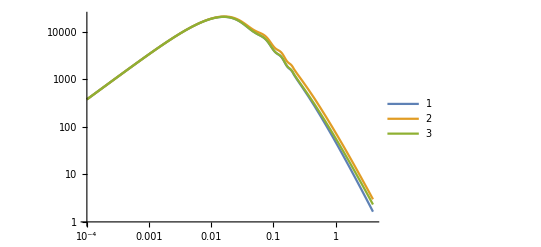

```mathematica
LogLogPlot[{pkLinInterp[0][0.25,kkk],pkLinInterp[4][0.25,kkk],pkLinInterp[6][0.25,kkk]}, {kkk,0.0001,4.0}, PlotLegends->Automatic]
```

```mathematica
Manipulate[LogLogPlot[{pkNonLinInterp[0][ztest,kkk],pkNonLinInterp[4][ztest,kkk],pkNonLinInterp[6][ztest,kkk]}, {kkk,0.0001,4.0}, PlotLegends->Automatic], {ztest, 0.001,10, 0.01}]
```

```mathematica
<<NumericalCalculus`
```

```mathematica
ClearAll[fgInterp]
```

```mathematica
fgInterp[mod_][z_, ka_]:=Block[{zz},-(1+z)*ND[Log[growthInterp[mod][zz,ka]],zz,z]]
```

```mathematica
redshiftsz[0]
```

{50.,49.4949,48.9899,48.4848,47.9798,47.4747,46.9697,46.4646,45.9596,45.4545,44.9495,44.4444,43.9394,43.4343,42.9293,42.4242,41.9192,41.4141,40.9091,40.404,39.899,39.3939,38.8889,38.3838,37.8788,37.3737,36.8687,36.3636,35.8586,35.3535,34.8485,34.3434,33.8384,33.3333,32.8283,32.3232,31.8182,31.3131,30.8081,30.303,29.798,29.2929,28.7879,28.2828,27.7778,27.2727,26.7677,26.2626,25.7576,25.2525,24.7475,24.2424,23.7374,23.2323,22.7273,22.2222,21.7172,21.2121,20.7071,20.202,19.697,19.1919,18.6869,18.1818,17.6768,17.1717,16.6667,16.1616,15.6566,15.1515,14.6465,14.1414,13.6364,13.1313,12.6263,12.1212,11.6162,11.1111,10.6061,10.101,9.59596,9.09091,8.58586,8.08081,7.57576,7.07071,6.56566,6.06061,5.55556,5.05051,4.54545,4.0404,3.53535,3.0303,2.52525,2.0202,1.51515,1.0101,0.505051,0.}

```mathematica
fgInterp[4][#,0.1]&/@redshiftsz[0]
```

{0.989442,0.989541,0.989641,0.989751,0.989859,0.989952,0.990064,0.990178,0.990269,0.990379,0.990485,0.990581,0.990692,0.990799,0.990899,0.991001,0.991107,0.991213,0.991321,0.991422,0.99152,0.991628,0.991738,0.991832,0.991943,0.992051,0.992145,0.992252,0.992355,0.992457,0.992565,0.992666,0.99277,0.992874,0.992972,0.993082,0.993184,0.993282,0.993385,0.99349,0.993593,0.993695,0.993797,0.993898,0.994002,0.994101,0.994201,0.994306,0.994403,0.994506,0.994605,0.994704,0.994807,0.994902,0.995003,0.995105,0.995196,0.995294,0.995391,0.995485,0.995581,0.995674,0.995767,0.995856,0.995948,0.996035,0.996119,0.996204,0.996286,0.996362,0.996436,0.996509,0.996573,0.996632,0.996687,0.996732,0.996768,0.996791,0.9968,0.996791,0.996754,0.996689,0.996591,0.996456,0.996268,0.996018,0.995686,0.995253,0.994697,0.994008,0.993199,0.992392,0.991836,0.992396,0.994498,0.998963,0.993993,0.966693,0.845876,0.609088}

```mathematica
manFzkFR=Manipulate[LogPlot[{fgInterp[0][zzz,kpoint],fgInterp[4][zzz,kpoint],fgInterp[6][zzz,kpoint]}, {zzz,0.,10.0}, PlotLegends->{"LCDM", "fR0=10^-4", "fR0=10^-6"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["z", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["k="<>ToString[N@kpoint]<>"  Mpc^-1", Bold, 14],Scaled[{0.8,0.2}]]    , PlotRange->{0.8,1.2}  ], {kpoint, 10^-4,2,0.001}]
```

```mathematica
Manipulate[LogPlot[{growthrateCAMBInterp[0][zzz,kpoint],growthrateCAMBInterp[4][zzz,kpoint],growthrateCAMBInterp[6][zzz,kpoint]}, {zzz,0.,10.0}, PlotLegends->{"LCDM", "fR0=10^-4", "fR0=10^-6"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["z", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["k="<>ToString[N@kpoint]<>"  Mpc^-1", Bold, 14],Scaled[{0.8,0.2}]]    , PlotRange->{0.8,1.2}  ], {kpoint, 10^-4,2,0.001}]
```

```mathematica
Manipulate[LogPlot[{growthrateCAMBInterp[4][zzz,kpoint],fgInterp[4][zzz,kpoint]}, {zzz,0.,10.0}, PlotLegends->{"f4-camb", "f4-deriv"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["z", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["k="<>ToString[N@kpoint]<>"  Mpc^-1", Bold, 14],Scaled[{0.8,0.2}]]    , PlotRange->All  ], {kpoint, 10^-4,2,0.001}]
```

```mathematica
Manipulate[LogPlot[{growthrateCAMBInterp[6][zzz,kpoint]/fgInterp[6][zzz,kpoint]}, {zzz,0.,10.0}, PlotLegends->{"f4-camb", "f4-deriv"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["z", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["k="<>ToString[N@kpoint]<>"  Mpc^-1", Bold, 14],Scaled[{0.8,0.2}]]    , PlotRange->All  ], {kpoint, 10^-4,2,0.001}]
```

```mathematica
ManToGif[manFzkFR,FileNameJoin[{NotebookDirectory[],"fG_zk-fR"}],1]
```

/local/home/scasas/CosmoProjects/cosmomathica/fG_zk-fR.gif

```mathematica
Manipulate[LogLinearPlot[{fgInterp[0][zpoint,kkk],fgInterp[4][zpoint,kkk],fgInterp[6][zpoint,kkk]}, {kkk,0.0001,4.0}, PlotLegends->{"LCDM", "fR0=10^-4", "fR0=10^-6"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["k", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["z="<>ToString[N@zpoint], Bold, 14],Scaled[{0.8,0.2}]]    (*PlotRange->{0.8,1.2}*)  ], {zpoint, 0.,9.9}]
```

```mathematica
s8growthrateInterp[4]
```

InterpolatingFunction[…]

```mathematica
s8growthrateInterp[4][0.24]
```

0.744024

```mathematica
Manipulate[LogPlot[{fgInterp[0][zzz,kpoint],fgInterp[4][zzz,kpoint],fgInterp[6][zzz,kpoint], s8growthrateInterp[4][zzz]}, {zzz,0.,10.0}, PlotLegends->{"LCDM", "logfR0=-4", "logfR0=-6", "k=s8_logfR0=-4"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["z", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["k="<>ToString[N@kpoint]<>"  Mpc^-1", Bold, 14],Scaled[{0.8,0.2}]]    , PlotRange->{0.8,1.2}  ], {kpoint, 10^-4,2,0.001}]
```

```mathematica
Manipulate[LogLinearPlot[{fgInterp[0][zpoint,kkk],fgInterp[4][zpoint,kkk],fgInterp[6][zpoint,kkk], s8growthrateInterp[4][zpoint]}, {kkk,0.0001,4.0}, PlotLegends->{"LCDM", "fR0=10^-4", "fR0=10^-6", "k=s8_logfR0=-4"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["k", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["z="<>ToString[N@zpoint], Bold, 14],Scaled[{0.8,0.2}]]    (*PlotRange->{0.8,1.2}*)  ], {zpoint, 0.,9.9}]
```

```mathematica
ClearAll[hofz]
```

```mathematica
hofz[0]=CAMB["H(z)"]/.cambdata[0]
```

{0.000997564,0.00082347,0.000663257,0.000518913,0.000393586,0.000292502,0.000223498}

There is a σ_8 for each redshift and for each spectral index

Plot the scalar angular power spectrum for TT

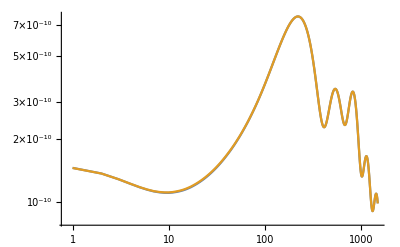

```mathematica
ListLogLogPlot[{(CAMB["CLscalar"]/.cambdata[0])[[1]],(CAMB["CLscalar"]/.cambdata[4])[[1]]} ,Joined->True]
```

Plot the scalar angular power spectrum for EE and TE

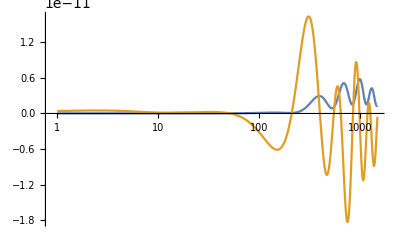

```mathematica
ListLogLinearPlot[(CAMB["CLscalar"]/.cambdata[0])[[2;;3]],Joined->True]
```

```mathematica
colorarra=ColorData["DarkRainbow"][#]&/@Subdivide[1,3]
```

{RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.33311066666666667, 0.5032283333333333, 0.26154733333333335],RGBColor[0.8562609999999999, 0.742794, 0.31908333333333333],RGBColor[0.72987, 0.239399, 0.230961]}

The results for the linear/nonlinear power spectrum as well as the transfer function contain a list for each redshift. Each one of those is a list of number pairs {k_i,P(k_i)} in the case of the power spectrum, and a list of seven numbers {k_i,T_1(k_i),..., T_6(k_i)} in case of the transfer function, each of which correspond to CDM, baryon, photon, massless neutrino, massive neutrinos, and total (massive).

Plot the nonlinear matter power spectrum for all redshifts

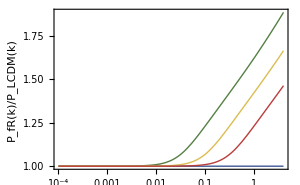

```mathematica
raplo=LogLinearPlot[Evaluate@(((pkLinInterp[#][0.,kkk]/pkLinInterp[0][0.,kkk])&/@{0,4,5,6})) (*PlotLegends->Placed[LineLegend[{"logfR0=-4,","logfR0=-5", "logfR0=-6", "LCDM"}], Scaled[{0.1,0.8}]]*),{kkk,0.0001,4}, Frame->True, FrameLabel->{"", Style["P_fR(k)/P_LCDM(k)", Bold, 10]} , ImageSize->{300,150}, FrameTicksStyle->Directive[Black,10], PlotStyle->Thread[{ConstantArray[Thick,Length@colorarra],colorarra}], PlotRange->All]
```

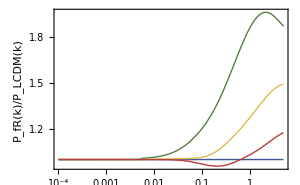

```mathematica
raplonl=LogLinearPlot[Evaluate@(((pkNonLinInterp[#][0.6,kkk]/pkNonLinInterp[0][0.6,kkk])&/@{0,4,5,6})) (*PlotLegends->Placed[LineLegend[{"logfR0=-4,","logfR0=-5", "logfR0=-6", "LCDM"}], Scaled[{0.1,0.8}]]*),{kkk,0.0001,5}, Frame->True, FrameLabel->{"", Style["P_fR(k)/P_LCDM(k)", Bold, 10]} , ImageSize->{300,150}, FrameTicksStyle->Directive[Black,10],
PlotStyle->Thread[{ConstantArray[Thick,Length@colorarra],colorarra}], PlotRange->All]
```

```mathematica
Thread[{ConstantArray[Thick,2*Length@colorarra],colorarra~Join~colorarra}]
```

{{Thickness[Large],RGBColor[0.237736, 0.340215, 0.575113]},{Thickness[Large],RGBColor[0.33311066666666667, 0.5032283333333333, 0.26154733333333335]},{Thickness[Large],RGBColor[0.8562609999999999, 0.742794, 0.31908333333333333]},{Thickness[Large],RGBColor[0.72987, 0.239399, 0.230961]},{Thickness[Large],RGBColor[0.237736, 0.340215, 0.575113]},{Thickness[Large],RGBColor[0.33311066666666667, 0.5032283333333333, 0.26154733333333335]},{Thickness[Large],RGBColor[0.8562609999999999, 0.742794, 0.31908333333333333]},{Thickness[Large],RGBColor[0.72987, 0.239399, 0.230961]}}

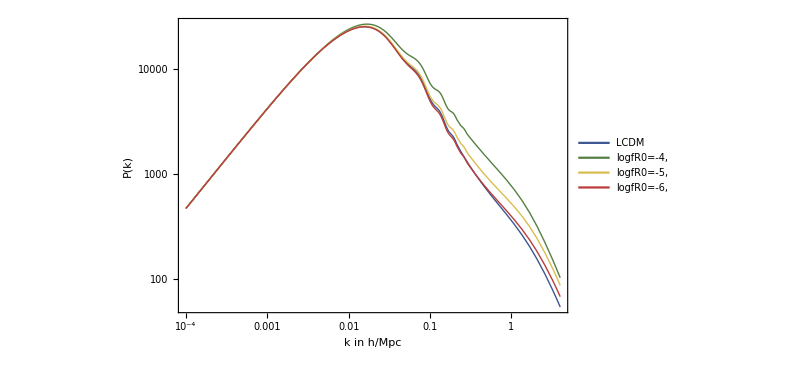

```mathematica
LogLogPlot[Evaluate@((pkNonLinInterp[#][0.,kkk]&/@{0,4,5,6})), {kkk,0.0001,4},PlotLegends->Placed[LineLegend[{"LCDM","logfR0=-4,","logfR0=-5,","logfR0=-6,"}], Scaled[{0.2,0.8}]], PlotStyle->Thread[{ConstantArray[Thick,2*Length@colorarra],colorarra~Join~colorarra}], Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],Epilog->Inset[raplonl, Scaled[{0.5,0.3}]]]
```

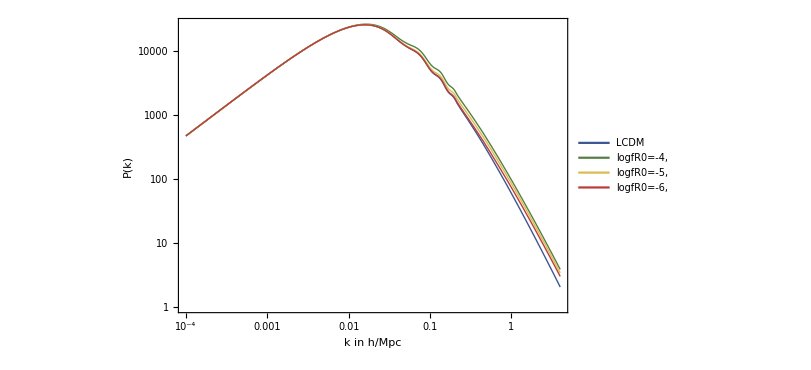

```mathematica
LogLogPlot[Evaluate@((pkLinInterp[#][0.,kkk]&/@{0,4,5,6})), {kkk,0.0001,4},PlotLegends->Placed[LineLegend[{"LCDM","logfR0=-4,","logfR0=-5,","logfR0=-6,"}], Scaled[{0.2,0.8}]], PlotStyle->Thread[{ConstantArray[Thick,2*Length@colorarra],colorarra~Join~colorarra}], Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],Epilog->Inset[raplo, Scaled[{0.5,0.3}]]]
```